```mathematica
Clear["Global`*"];
SeedRandom[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler4`";
dKdq[p_,q_]=0;
```

```mathematica
ρ=1-1/10^13;
SIGMA={{1,ρ},{ρ,1}};
U[x_,y_]=N[1/2 Simplify[{x,y}.LinearSolve[SIGMA,{x,y}]]];
dU[x_,y_]=GradientG[U[x,y],{x,y}];
ddU[x_,y_]=HessianH[U[x,y],{x,y}];
dddU[x_,y_]=D3[U[x,y],{x,y}];
Dim=2;
```

```mathematica
QS=hmc[Dim,5000,10000,{}];
```

1001750224.2.714690.6769150.55960.574509{1,4,5}{1,4,6}0.000581829825247.0.000581829TrueFalse

20021.0819×10^72.133610.2842510.2099271.24811{1,3}{6}0.0001392851.0819×10^70.000139285FalseFalse

30031.71624×10^81.988780.3426670.5692672.32349{1,4}{1,6}0.00002505171.56021×10^80.0000250517FalseTrue

40043.34446×10^83.904420.5646580.4689370.921326{1,3}{6}0.00001882173.34446×10^80.0000188217FalseFalse

50058.28946×10^111.250280.05234270.06679512.38596{2,4,6}{1,6}4.5745×10^-78.28946×10^114.5745×10^-7TrueFalse

60068.28946×10^110.2456820.0757640.08771132.71986{2,4,6}{1,6}4.5745×10^-78.28946×10^114.5745×10^-7TrueFalse

70078.28946×10^112.4720.6184430.5399673.3147{2,4,6}{1,6}4.5745×10^-78.28946×10^114.5745×10^-7TrueFalse

80088.28946×10^111.308850.4067620.5171761.64671{2,4,6}{1,6}4.5745×10^-78.28946×10^114.5745×10^-7TrueFalse

90098.28946×10^111.914430.6474510.3063193.0918{2,4,6}{1,6}4.5745×10^-78.28946×10^114.5745×10^-7TrueFalse

{1.0006,0.993219}

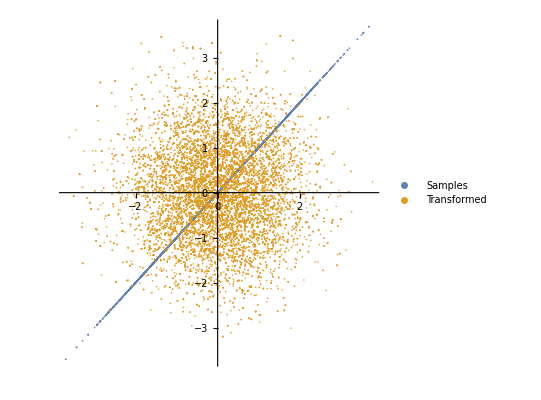

```mathematica
QS1=QS.MatrixPower[SIGMA,-.5];
StandardDeviation[QS1]
ListPlot[{QS,QS1},PlotStyle->Opacity[1],AspectRatio->1,PlotLegends->{Samples, Transformed}]
```